```mathematica
A2Lattice = Flatten[Table[If[a+b+c==0&&1/2(a^2+b^2+c^2)≤2,{a,b,c},Nothing],{a,-3,3},{b,-3,3},{c,-3,3}],2];
A2Roots = Table[If[1/2a.a ==1,a,Nothing],{a,A2Lattice}];
l[ϵ1_,ϵ2_,σ1_,σ2_,σ3_,k1_,k2_,k3_,a1_,a2_,a3_]:=Product[Which[{k1,k2,k3}.{a1,a2,a3}<0&&i+j≤-{k1,k2,k3}.{a1,a2,a3}-1,(-ϵ1 i-ϵ2 j+{a1,a2,a3}.{σ1,σ2,σ3}),{k1,k2,k3}.{a1,a2,a3}>1&&i+j≤{k1,k2,k3}.{a1,a2,a3}-2,(ϵ1(i+1)+ϵ2(j+1)+{a1,a2,a3}.{σ1,σ2,σ3}),True,1],{i,0,2},{j,0,2}];
l[ϵ1_,ϵ2_,{σ1_,σ2_,σ3_},{k1_,k2_,k3_},{a1_,a2_,a3_}]:=l[ϵ1,ϵ2,σ1,σ2,σ3,k1,k2,k3,a1,a2,a3];
L[ϵ1_,ϵ2_,{σ1_,σ2_,σ3_},{k1_,k2_,k3_}]:=Product[l[ϵ1,ϵ2,{σ1,σ2,σ3},{k1,k2,k3},a],{a,A2Roots}]//Cancel;
Subscript[Ž, 1][ϵ1_,ϵ2_,{σ1_,σ2_,σ3_}]:=1/(-ϵ1 ϵ2)Sum[(1/((+ϵ1+ϵ2+{σ1,σ2,σ3}.a)({σ1,σ2,σ3}.a)Product[If[ b.a==1, {σ1,σ2,σ3}.b,1],{b,A2Roots}]))//Cancel,{a,A2Roots}];
σ:={σ1,σ2,σ3};
```

```mathematica
(ϵ Subscript[Ž, 1][ϵ,ℏ,{a1,a2,a3}]//Simplify)/.{a1->I a1,a2->I a2,a3->I a3,ϵ->0}//FullSimplify
```

(2 (a1^2+a2^2-a2 a3+a3^2-a1 (a2+a3)+3 ℏ^2))/(ℏ ((a1-a2)^2+ℏ^2) ((a1-a3)^2+ℏ^2) ((a2-a3)^2+ℏ^2))

```mathematica
(ϵ Subscript[Ž, 1][ϵ,ℏ,{a1,a2,a3}]//Simplify)/.{a1->I a1,a2->I a2,a3->-I a1-I a2,ϵ->0}//FullSimplify
```

(6 (a1^2+a1 a2+a2^2+ℏ^2))/(ℏ ((a1-a2)^2+ℏ^2) ((2 a1+a2)^2+ℏ^2) ((a1+2 a2)^2+ℏ^2))

```mathematica
Subscript[z, n_][ϵ1_,ϵ2_,{σ1_,σ2_,σ3_}]:=1/(n^2 ϵ1 ϵ2)Sum[If[1/2 k.k + m1+m2 == n,((ϵ1 m1+(ϵ1+ϵ2) m2+k.{σ1,σ2,σ3}+k.k/2(2ϵ1+ϵ2))(ϵ1 m1+(ϵ1+ϵ2) m2+k.{σ1,σ2,σ3}+k.k/2(2ϵ1+ϵ2)-n(ϵ1+ϵ2)))/L[ϵ1,ϵ1+ϵ2,{σ1,σ2,σ3},k] If[m1==0,1,Subscript[z, m1][ϵ1,ϵ2,{σ1,σ2,σ3}+ϵ1 k]]If[m2==0,1,Subscript[z, m2][-ϵ2,ϵ1+ϵ2,{σ1,σ2,σ3}+ϵ1 k+ϵ2 k]]//Cancel,0],{k,A2Lattice},{m1,0,n-1},{m2,0,n-1}]
```

```mathematica
ztable = Join[{1},Table[( Subscript[z, n][ϵ,ℏ,{a1,a2,a3}]//Cancel)/.{a1->I A1,a2->I A2,a3->I A3},{n,1,2}]];
```

```mathematica
wtable = ((CoefficientList[Series[ϵ Log[Sum[ztable[[n]] q^(n-1),{n,1,Length[ztable]}]],{q,0,Length[ztable]-1}],q]//Cancel)/.ϵ->0)//Cancel;
```

```mathematica
Sum[wtable[[n]]q^(n-1),{n,1,Length[wtable]}]
```

(2 q (A1^2-A1 A2+A2^2-A1 A3-A2 A3+A3^2+3 ℏ^2))/(ℏ (ⅈ A1-ⅈ A2+ℏ) (-ⅈ A1+ⅈ A2+ℏ) (ⅈ A1-ⅈ A3+ℏ) (ⅈ A2-ⅈ A3+ℏ) (-ⅈ A1+ⅈ A3+ℏ) (-ⅈ A2+ⅈ A3+ℏ))+(q^2 (5 A1^12 A2^2-30 A1^11 A2^3+74 A1^10 A2^4-95 A1^9 A2^5+74 A1^8 A2^6-56 A1^7 A2^7+74 A1^6 A2^8-95 A1^5 A2^9+74 A1^4 A2^10-30 A1^3 A2^11+5 A1^2 A2^12-10 A1^12 A2 A3+30 A1^11 A2^2 A3+34 A1^10 A2^3 A3-265 A1^9 A2^4 A3+411 A1^8 A2^5 A3-200 A1^7 A2^6 A3-200 A1^6 A2^7 A3+411 A1^5 A2^8 A3-265 A1^4 A2^9 A3+34 A1^3 A2^10 A3+30 A1^2 A2^11 A3-10 A1 A2^12 A3+5 A1^12 A3^2+30 A1^11 A2 A3^2-216 A1^10 A2^2 A3^2+360 A1^9 A2^3 A3^2+165 A1^8 A2^4 A3^2-1044 A1^7 A2^5 A3^2+1400 A1^6 A2^6 A3^2-1044 A1^5 A2^7 A3^2+165 A1^4 A2^8 A3^2+360 A1^3 A2^9 A3^2-216 A1^2 A2^10 A3^2+30 A1 A2^11 A3^2+5 A2^12 A3^2-30 A1^11 A3^3+34 A1^10 A2 A3^3+360 A1^9 A2^2 A3^3-1300 A1^8 A2^3 A3^3+1300 A1^7 A2^4 A3^3-364 A1^6 A2^5 A3^3-364 A1^5 A2^6 A3^3+1300 A1^4 A2^7 A3^3-1300 A1^3 A2^8 A3^3+360 A1^2 A2^9 A3^3+34 A1 A2^10 A3^3-30 A2^11 A3^3+74 A1^10 A3^4-265 A1^9 A2 A3^4+165 A1^8 A2^2 A3^4+1300 A1^7 A2^3 A3^4-1820 A1^6 A2^4 A3^4+1092 A1^5 A2^5 A3^4-1820 A1^4 A2^6 A3^4+1300 A1^3 A2^7 A3^4+165 A1^2 A2^8 A3^4-265 A1 A2^9 A3^4+74 A2^10 A3^4-95 A1^9 A3^5+411 A1^8 A2 A3^5-1044 A1^7 A2^2 A3^5-364 A1^6 A2^3 A3^5+1092 A1^5 A2^4 A3^5+1092 A1^4 A2^5 A3^5-364 A1^3 A2^6 A3^5-1044 A1^2 A2^7 A3^5+411 A1 A2^8 A3^5-95 A2^9 A3^5+74 A1^8 A3^6-200 A1^7 A2 A3^6+1400 A1^6 A2^2 A3^6-364 A1^5 A2^3 A3^6-1820 A1^4 A2^4 A3^6-364 A1^3 A2^5 A3^6+1400 A1^2 A2^6 A3^6-200 A1 A2^7 A3^6+74 A2^8 A3^6-56 A1^7 A3^7-200 A1^6 A2 A3^7-1044 A1^5 A2^2 A3^7+1300 A1^4 A2^3 A3^7+1300 A1^3 A2^4 A3^7-1044 A1^2 A2^5 A3^7-200 A1 A2^6 A3^7-56 A2^7 A3^7+74 A1^6 A3^8+411 A1^5 A2 A3^8+165 A1^4 A2^2 A3^8-1300 A1^3 A2^3 A3^8+165 A1^2 A2^4 A3^8+411 A1 A2^5 A3^8+74 A2^6 A3^8-95 A1^5 A3^9-265 A1^4 A2 A3^9+360 A1^3 A2^2 A3^9+360 A1^2 A2^3 A3^9-265 A1 A2^4 A3^9-95 A2^5 A3^9+74 A1^4 A3^10+34 A1^3 A2 A3^10-216 A1^2 A2^2 A3^10+34 A1 A2^3 A3^10+74 A2^4 A3^10-30 A1^3 A3^11+30 A1^2 A2 A3^11+30 A1 A2^2 A3^11-30 A2^3 A3^11+5 A1^2 A3^12-10 A1 A2 A3^12+5 A2^2 A3^12-7 A1^12 ℏ^2+42 A1^11 A2 ℏ^2-31 A1^10 A2^2 ℏ^2-230 A1^9 A2^3 ℏ^2+707 A1^8 A2^4 ℏ^2-986 A1^7 A2^5 ℏ^2+1003 A1^6 A2^6 ℏ^2-986 A1^5 A2^7 ℏ^2+707 A1^4 A2^8 ℏ^2-230 A1^3 A2^9 ℏ^2-31 A1^2 A2^10 ℏ^2+42 A1 A2^11 ℏ^2-7 A2^12 ℏ^2+42 A1^11 A3 ℏ^2-400 A1^10 A2 A3 ℏ^2+1000 A1^9 A2^2 A3 ℏ^2-758 A1^8 A2^3 A3 ℏ^2-726 A1^7 A2^4 A3 ℏ^2+884 A1^6 A2^5 A3 ℏ^2+884 A1^5 A2^6 A3 ℏ^2-726 A1^4 A2^7 A3 ℏ^2-758 A1^3 A2^8 A3 ℏ^2+1000 A1^2 A2^9 A3 ℏ^2-400 A1 A2^10 A3 ℏ^2+42 A2^11 A3 ℏ^2-31 A1^10 A3^2 ℏ^2+1000 A1^9 A2 A3^2 ℏ^2-3363 A1^8 A2^2 A3^2 ℏ^2+4484 A1^7 A2^3 A3^2 ℏ^2+331 A1^6 A2^4 A3^2 ℏ^2-5304 A1^5 A2^5 A3^2 ℏ^2+331 A1^4 A2^6 A3^2 ℏ^2+4484 A1^3 A2^7 A3^2 ℏ^2-3363 A1^2 A2^8 A3^2 ℏ^2+1000 A1 A2^9 A3^2 ℏ^2-31 A2^10 A3^2 ℏ^2-230 A1^9 A3^3 ℏ^2-758 A1^8 A2 A3^3 ℏ^2+4484 A1^7 A2^2 A3^3 ℏ^2-10904 A1^6 A2^3 A3^3 ℏ^2+8178 A1^5 A2^4 A3^3 ℏ^2+8178 A1^4 A2^5 A3^3 ℏ^2-10904 A1^3 A2^6 A3^3 ℏ^2+4484 A1^2 A2^7 A3^3 ℏ^2-758 A1 A2^8 A3^3 ℏ^2-230 A2^9 A3^3 ℏ^2+707 A1^8 A3^4 ℏ^2-726 A1^7 A2 A3^4 ℏ^2+331 A1^6 A2^2 A3^4 ℏ^2+8178 A1^5 A2^3 A3^4 ℏ^2-20445 A1^4 A2^4 A3^4 ℏ^2+8178 A1^3 A2^5 A3^4 ℏ^2+331 A1^2 A2^6 A3^4 ℏ^2-726 A1 A2^7 A3^4 ℏ^2+707 A2^8 A3^4 ℏ^2-986 A1^7 A3^5 ℏ^2+884 A1^6 A2 A3^5 ℏ^2-5304 A1^5 A2^2 A3^5 ℏ^2+8178 A1^4 A2^3 A3^5 ℏ^2+8178 A1^3 A2^4 A3^5 ℏ^2-5304 A1^2 A2^5 A3^5 ℏ^2+884 A1 A2^6 A3^5 ℏ^2-986 A2^7 A3^5 ℏ^2+1003 A1^6 A3^6 ℏ^2+884 A1^5 A2 A3^6 ℏ^2+331 A1^4 A2^2 A3^6 ℏ^2-10904 A1^3 A2^3 A3^6 ℏ^2+331 A1^2 A2^4 A3^6 ℏ^2+884 A1 A2^5 A3^6 ℏ^2+1003 A2^6 A3^6 ℏ^2-986 A1^5 A3^7 ℏ^2-726 A1^4 A2 A3^7 ℏ^2+4484 A1^3 A2^2 A3^7 ℏ^2+4484 A1^2 A2^3 A3^7 ℏ^2-726 A1 A2^4 A3^7 ℏ^2-986 A2^5 A3^7 ℏ^2+707 A1^4 A3^8 ℏ^2-758 A1^3 A2 A3^8 ℏ^2-3363 A1^2 A2^2 A3^8 ℏ^2-758 A1 A2^3 A3^8 ℏ^2+707 A2^4 A3^8 ℏ^2-230 A1^3 A3^9 ℏ^2+1000 A1^2 A2 A3^9 ℏ^2+1000 A1 A2^2 A3^9 ℏ^2-230 A2^3 A3^9 ℏ^2-31 A1^2 A3^10 ℏ^2-400 A1 A2 A3^10 ℏ^2-31 A2^2 A3^10 ℏ^2+42 A1 A3^11 ℏ^2+42 A2 A3^11 ℏ^2-7 A3^12 ℏ^2-93 A1^10 ℏ^4+465 A1^9 A2 ℏ^4-453 A1^8 A2^2 ℏ^4-978 A1^7 A2^3 ℏ^4+3351 A1^6 A2^4 ℏ^4-4677 A1^5 A2^5 ℏ^4+3351 A1^4 A2^6 ℏ^4-978 A1^3 A2^7 ℏ^4-453 A1^2 A2^8 ℏ^4+465 A1 A2^9 ℏ^4-93 A2^10 ℏ^4+465 A1^9 A3 ℏ^4-3279 A1^8 A2 A3 ℏ^4+6558 A1^7 A2^2 A3 ℏ^4-6558 A1^6 A2^3 A3 ℏ^4+3279 A1^5 A2^4 A3 ℏ^4+3279 A1^4 A2^5 A3 ℏ^4-6558 A1^3 A2^6 A3 ℏ^4+6558 A1^2 A2^7 A3 ℏ^4-3279 A1 A2^8 A3 ℏ^4+465 A2^9 A3 ℏ^4-453 A1^8 A3^2 ℏ^4+6558 A1^7 A2 A3^2 ℏ^4-13116 A1^6 A2^2 A3^2 ℏ^4+13116 A1^5 A2^3 A3^2 ℏ^4-16395 A1^4 A2^4 A3^2 ℏ^4+13116 A1^3 A2^5 A3^2 ℏ^4-13116 A1^2 A2^6 A3^2 ℏ^4+6558 A1 A2^7 A3^2 ℏ^4-453 A2^8 A3^2 ℏ^4-978 A1^7 A3^3 ℏ^4-6558 A1^6 A2 A3^3 ℏ^4+13116 A1^5 A2^2 A3^3 ℏ^4+13116 A1^2 A2^5 A3^3 ℏ^4-6558 A1 A2^6 A3^3 ℏ^4-978 A2^7 A3^3 ℏ^4+3351 A1^6 A3^4 ℏ^4+3279 A1^5 A2 A3^4 ℏ^4-16395 A1^4 A2^2 A3^4 ℏ^4-16395 A1^2 A2^4 A3^4 ℏ^4+3279 A1 A2^5 A3^4 ℏ^4+3351 A2^6 A3^4 ℏ^4-4677 A1^5 A3^5 ℏ^4+3279 A1^4 A2 A3^5 ℏ^4+13116 A1^3 A2^2 A3^5 ℏ^4+13116 A1^2 A2^3 A3^5 ℏ^4+3279 A1 A2^4 A3^5 ℏ^4-4677 A2^5 A3^5 ℏ^4+3351 A1^4 A3^6 ℏ^4-6558 A1^3 A2 A3^6 ℏ^4-13116 A1^2 A2^2 A3^6 ℏ^4-6558 A1 A2^3 A3^6 ℏ^4+3351 A2^4 A3^6 ℏ^4-978 A1^3 A3^7 ℏ^4+6558 A1^2 A2 A3^7 ℏ^4+6558 A1 A2^2 A3^7 ℏ^4-978 A2^3 A3^7 ℏ^4-453 A1^2 A3^8 ℏ^4-3279 A1 A2 A3^8 ℏ^4-453 A2^2 A3^8 ℏ^4+465 A1 A3^9 ℏ^4+465 A2 A3^9 ℏ^4-93 A3^10 ℏ^4-450 A1^8 ℏ^6+1800 A1^7 A2 ℏ^6-744 A1^6 A2^2 ℏ^6-4068 A1^5 A2^3 ℏ^6+6474 A1^4 A2^4 ℏ^6-4068 A1^3 A2^5 ℏ^6-744 A1^2 A2^6 ℏ^6+1800 A1 A2^7 ℏ^6-450 A2^8 ℏ^6+1800 A1^7 A3 ℏ^6-11112 A1^6 A2 A3 ℏ^6+16668 A1^5 A2^2 A3 ℏ^6-5556 A1^4 A2^3 A3 ℏ^6-5556 A1^3 A2^4 A3 ℏ^6+16668 A1^2 A2^5 A3 ℏ^6-11112 A1 A2^6 A3 ℏ^6+1800 A2^7 A3 ℏ^6-744 A1^6 A3^2 ℏ^6+16668 A1^5 A2 A3^2 ℏ^6-33336 A1^4 A2^2 A3^2 ℏ^6+22224 A1^3 A2^3 A3^2 ℏ^6-33336 A1^2 A2^4 A3^2 ℏ^6+16668 A1 A2^5 A3^2 ℏ^6-744 A2^6 A3^2 ℏ^6-4068 A1^5 A3^3 ℏ^6-5556 A1^4 A2 A3^3 ℏ^6+22224 A1^3 A2^2 A3^3 ℏ^6+22224 A1^2 A2^3 A3^3 ℏ^6-5556 A1 A2^4 A3^3 ℏ^6-4068 A2^5 A3^3 ℏ^6+6474 A1^4 A3^4 ℏ^6-5556 A1^3 A2 A3^4 ℏ^6-33336 A1^2 A2^2 A3^4 ℏ^6-5556 A1 A2^3 A3^4 ℏ^6+6474 A2^4 A3^4 ℏ^6-4068 A1^3 A3^5 ℏ^6+16668 A1^2 A2 A3^5 ℏ^6+16668 A1 A2^2 A3^5 ℏ^6-4068 A2^3 A3^5 ℏ^6-744 A1^2 A3^6 ℏ^6-11112 A1 A2 A3^6 ℏ^6-744 A2^2 A3^6 ℏ^6+1800 A1 A3^7 ℏ^6+1800 A2 A3^7 ℏ^6-450 A3^8 ℏ^6-922 A1^6 ℏ^8+2766 A1^5 A2 ℏ^8-879 A1^4 A2^2 ℏ^8-2852 A1^3 A2^3 ℏ^8-879 A1^2 A2^4 ℏ^8+2766 A1 A2^5 ℏ^8-922 A2^6 ℏ^8+2766 A1^5 A3 ℏ^8-12072 A1^4 A2 A3 ℏ^8+12072 A1^3 A2^2 A3 ℏ^8+12072 A1^2 A2^3 A3 ℏ^8-12072 A1 A2^4 A3 ℏ^8+2766 A2^5 A3 ℏ^8-879 A1^4 A3^2 ℏ^8+12072 A1^3 A2 A3^2 ℏ^8-36216 A1^2 A2^2 A3^2 ℏ^8+12072 A1 A2^3 A3^2 ℏ^8-879 A2^4 A3^2 ℏ^8-2852 A1^3 A3^3 ℏ^8+12072 A1^2 A2 A3^3 ℏ^8+12072 A1 A2^2 A3^3 ℏ^8-2852 A2^3 A3^3 ℏ^8-879 A1^2 A3^4 ℏ^8-12072 A1 A2 A3^4 ℏ^8-879 A2^2 A3^4 ℏ^8+2766 A1 A3^5 ℏ^8+2766 A2 A3^5 ℏ^8-922 A3^6 ℏ^8-1659 A1^4 ℏ^10+3318 A1^3 A2 ℏ^10-4977 A1^2 A2^2 ℏ^10+3318 A1 A2^3 ℏ^10-1659 A2^4 ℏ^10+3318 A1^3 A3 ℏ^10+3318 A2^3 A3 ℏ^10-4977 A1^2 A3^2 ℏ^10-4977 A2^2 A3^2 ℏ^10+3318 A1 A3^3 ℏ^10+3318 A2 A3^3 ℏ^10-1659 A3^4 ℏ^10-3081 A1^2 ℏ^12+3081 A1 A2 ℏ^12-3081 A2^2 ℏ^12+3081 A1 A3 ℏ^12+3081 A2 A3 ℏ^12-3081 A3^2 ℏ^12-1980 ℏ^14))/(ℏ (ⅈ A1-ⅈ A2+ℏ)^3 (-ⅈ A1+ⅈ A2+ℏ)^3 (ⅈ A1-ⅈ A3+ℏ)^3 (ⅈ A2-ⅈ A3+ℏ)^3 (-ⅈ A1+ⅈ A3+ℏ)^3 (-ⅈ A2+ⅈ A3+ℏ)^3 (ⅈ A1-ⅈ A2+2 ℏ) (-ⅈ A1+ⅈ A2+2 ℏ) (ⅈ A1-ⅈ A3+2 ℏ) (ⅈ A2-ⅈ A3+2 ℏ) (-ⅈ A1+ⅈ A3+2 ℏ) (-ⅈ A2+ⅈ A3+2 ℏ))

```mathematica
((2 q (A1^2-A1 A2+A2^2-A1 A3-A2 A3+A3^2+3 ℏ^2))/(ℏ (ⅈ A1-ⅈ A2+ℏ) (-ⅈ A1+ⅈ A2+ℏ) (ⅈ A1-ⅈ A3+ℏ) (ⅈ A2-ⅈ A3+ℏ) (-ⅈ A1+ⅈ A3+ℏ) (-ⅈ A2+ⅈ A3+ℏ))/.{A2->0,A3->-A3})//FullSimplify
```

(2 q (A1^2+A1 A3+A3^2+3 ℏ^2))/(ℏ (A1^2+ℏ^2) (A3^2+ℏ^2) ((A1+A3)^2+ℏ^2))

```mathematica
Subscript[W, inst][A1_,A2_,A3_,ℏ_,q_]:=(2 q (A1^2+A2^2-A2 A3+A3^2-A1 (A2+A3)+3 ℏ^2))/(ℏ ((A1-A2)^2+ℏ^2) ((A1-A3)^2+ℏ^2) ((A2-A3)^2+ℏ^2));
γ4d[x_,ℏ_]:=x Log[(Q^(1/6)/ℏ)^2] - (π ℏ)/4-(I ℏ)/2 Log[Gamma[1+I x/ℏ]/Gamma[1-I x/ℏ]] 
Subscript[dW, pert][i_,A1_,A2_,A3_,ℏ_,q_]:=((Log[(Q^(1/6)/ℏ)^2] Subscript[a, i])+2ℏ  I Log[Product[If[j≠i,-Gamma[1+I (Subscript[a, i]-Subscript[a, j])/h]/Gamma[1-I (Subscript[a, i]-Subscript[a, j])/h],1],{j,1,3}]])/.{Subscript[a, 1]->A1,Subscript[a, 2]->A2,Subscript[a, 3]->A3};
```

```mathematica
γ4d[x_,ℏ_]:=x Log[(Q^(1/6)/ℏ)^2] - (π ℏ)/4-(I ℏ)/2 Log[Gamma[1+I x/ℏ]/Gamma[1-I x/ℏ]] ;
rhoA2 = {2,1,0};
```

```mathematica
(Sum[γ4d[{a1,a2,-a1-a2}.α,ℏ]α,{α,A2Roots}]-π ℏ rhoA2)[[1]]
```

-2 π ℏ-(-2 a1-a2) Log[1/(13^(1/3) ℏ^2)]+(a1-a2) Log[1/(13^(1/3) ℏ^2)]-(-a1+a2) Log[1/(13^(1/3) ℏ^2)]+(2 a1+a2) Log[1/(13^(1/3) ℏ^2)]+1/2 ⅈ ℏ Log[Gamma[1+(ⅈ (-2 a1-a2))/ℏ]/Gamma[1-(ⅈ (-2 a1-a2))/ℏ]]-1/2 ⅈ ℏ Log[Gamma[1+(ⅈ (a1-a2))/ℏ]/Gamma[1-(ⅈ (a1-a2))/ℏ]]+1/2 ⅈ ℏ Log[Gamma[1+(ⅈ (-a1+a2))/ℏ]/Gamma[1-(ⅈ (-a1+a2))/ℏ]]-1/2 ⅈ ℏ Log[Gamma[1+(ⅈ (2 a1+a2))/ℏ]/Gamma[1-(ⅈ (2 a1+a2))/ℏ]]

```mathematica
atable ={a1,a2,-a1-a2}/.(Flatten[Table[FindRoot[{(Sum[γ4d[{a1,a2,-a1-a2}.α,h]α,{α,A2Roots}]-π h rhoA2)[[1]]+(D[Subscript[W, inst][α,a2,-α-a2,h,Q],α]/.α->a1)+2 π h n1,(Sum[γ4d[{a1,a2,-a1-a2}.α,h]α,{α,A2Roots}]-π h rhoA2)[[2]]+(D[Subscript[W, inst][a1,α,-a1-α,h,Q],α]/.α->a2)+2 π h n2},{{a1,0.,10},{a2,0.,10}}],{n1,-2,2},{n2,2,2}],1]//Chop//DeleteDuplicates)
Table[1/2(a[[1]]^2+a[[2]]^2+a[[3]]^2)+(Q D[Subscript[W, inst][a[[1]],a[[2]],a[[3]],h,q],q]/.q->Q),{a,atable}]//Chop//Sort
vals
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{-4.7317,2.36403,2.36767},{-1.95949,1.4314,0.528082},{-0.836583,1.26708,-0.430498},{-0.000767528,1.30987,-1.30911},{1.25105,1.72433,-2.97538}}

{1.25835,1.72328,3.0883,6.69795,16.7927}

{5.33338,8.59121,10.8747,12.1136,14.9961,15.8949}

```mathematica
NIntegrate[Sin[x],{x,I 0.001 + 0.,I 0.001 + 1.}]
```

0.459698+0.000841471 ⅈ

```mathematica
Sin[I 0.001 +y]//Simplify//Chop
```

(0.+0.001 ⅈ) Cos[y]+1. Sin[y]

```mathematica
atable ={a1,-a1}/.(Flatten[Table[FindRoot[{(Sum[γ4d[{a1,-a1}.α,h]α,{α,A1Roots}]-π h {1,0})[[1]]+(D[Subscript[W, inst][α,-α,h,Q],α]/.α->a1)+2 π h n1},{a1,0.,10}],{n1,-2,2}],0]//Chop//DeleteDuplicates)
Table[1/2(a[[1]]^2+a[[2]]^2)+(Q D[Subscript[W, inst][a[[1]],a[[2]],h,q],q]/.q->Q),{a,atable}]//Chop//Sort
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{{-4.04696,4.04696},{-2.5798,2.5798},{-0.566519,0.566519},{0.566519,-0.566519},{2.5798,-2.5798}}

{0.349806,0.349806,6.65893,6.65893,16.3794}

```mathematica
Clear[Q,h]
```

```mathematica
nmax=6;
V[x1_,x2_]:=E^(x1-x2)+E^(x2-(-x1-x2))+Q E^((-x1-x2)-x1)
L=15;
h=1.5; 
Q=1/13;
ℒ=-h^2*Laplacian[u[x1,x2],{x1,x2}]+V[x1,x2]*u[x1,x2];
{vals,funs}=NDEigensystem[{ℒ},{u},{x1,x2}∈Disk[{0,0},L],nmax,Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.05}}}}];
vals
Table[Plot3D[funs⟦i⟧[x,y],{x,y}∈Disk[{0,0},L],PlotRange->All,PlotLabel->vals⟦i⟧,PlotTheme->"Minimal"],{i,Length[vals]}]
```

{5.33338,8.59121,10.8747,12.1136,14.9961,15.8949}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Show[Show[Table[Plot3D[h* funs[[i]][x,y]+vals[[i]],{x,y}∈Disk[{0,0},L]],{i,Length[vals]}] ],Plot3D[V[x,y],{x,y}∈Disk[{0,0},L]]]
```

-Graphics3D-

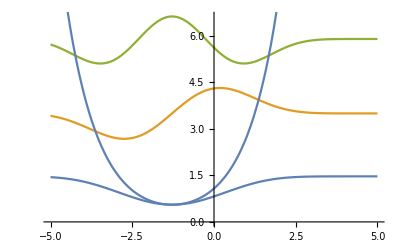

```mathematica
NDEigensystem
```

```mathematica
atable ={a1,a2,-a1-a2}/.(Flatten[Table[FindRoot[{Subscript[dW, pert][1,a1,a2,-a1-a2,h,Q]+(D[Subscript[W, inst][α,a2,-α-a2,h,Q],α]/.α->a1)+2 π h n1,Subscript[dW, pert][2,a1,a2,-a1-a2,h,Q]+(D[Subscript[W, inst][a1,α,-a1-α,h,Q],α]/.α->a2)+2 π h n2},{{a1,0.,10},{a2,0.,10}}],{n1,0,2},{n2,0,2}],1]//Chop//DeleteDuplicates);
Table[If[Im[a]=={0,0,0},a,Nothing],{a,atable}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{0,0,0},{-2.4119,6.18454,-3.77264},{-4.35295,6.55767,-2.20473},{3.61066,-0.000406423,-3.61026},{3.28803,3.28803,-6.57605},{4.91769,8.32168,-13.2394},{7.12774,-9.51412×10^-6,-7.12773},{7.77815,4.30892,-12.0871},{8.38848,8.38848,-16.777}}

```mathematica
Table[1/2(a[[1]]^2+a[[2]]^2+a[[3]]^2)+(Q D[Subscript[W, inst][a[[1]],a[[2]],a[[3]],h,q],q]/.q->Q),{a,atable}]//Chop//Sort
vals
```

{1.58025,13.045,29.1573,32.4458,33.4104,50.8054,112.582,134.358,211.102}

{10.2469,15.3005,18.872,20.6504}

```mathematica
Flatten[Table[FindRoot[{Subscript[dW, pert][1,a1,a2,-a1-a2,h,Q]+(D[Subscript[W, inst][α,a2,-α-a2,h,Q],α]/.α->a1)+2 π h n1,Subscript[dW, pert][2,a1,a2,-a1-a2,h,Q]+(D[Subscript[W, inst][a1,α,-a1-α,h,Q],α]/.α->a2)+2 π h n2},{{a1,0},{a2,0}}],{n1,1,3},{n2,1,3}],1]//DeleteDuplicates
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{a1→0.031824-0.587899 ⅈ,a2→0.031824-0.587899 ⅈ},{a1→0.773323+0.956503 ⅈ,a2→3.49429+0.661987 ⅈ},{a1→2.19551-0.472627 ⅈ,a2→3.77658+2.06685 ⅈ},{a1→3.49429+0.661987 ⅈ,a2→0.773323+0.956503 ⅈ},{a1→3.4274+0.640812 ⅈ,a2→3.4274+0.640812 ⅈ},{a1→6.45247-0.0424788 ⅈ,a2→11.3068-0.649879 ⅈ},{a1→3.77658+2.06685 ⅈ,a2→2.19551-0.472627 ⅈ},{a1→11.3068-0.649879 ⅈ,a2→6.45247-0.0424788 ⅈ},{a1→6.7513+0.369977 ⅈ,a2→6.7513+0.369977 ⅈ}}

```mathematica
Subscript[dW, pert][i_,Subscript[a, 1]_,Subscript[a, 2]_,Subscript[a, 2]_,ℏ_,q_]:=((Log[(Q^(1/6)/ℏ)^2]2 Subscript[a, i])+ℏ Log[Product[If[j≠i,-Gamma[1+I (Subscript[a, i]-Subscript[a, j])/h]/Gamma[1-I (Subscript[a, i]-Subscript[a, j])/h],1],{j,1,3}]]);
```